## Opakování

Pomocí funkce Plot3D vytvořte graf odpovídající předpisu z=x^3. y^3 spadající do intervalu x ϵ (0,10) a y ϵ (0,10). V tomto grafu budou naformátovány následující styly. Osy (x,y,z) budou tečkované, červené a bude také nastavena jejich tloušťka. Jejich počátek bude nastaven do bodu podle souřadnic (1,2,3). Název grafu bude orámovaný, písmu bude nastavena větší velikost, styl Italic, barva a tloušťka. Mřížka grafu nebude vykreslena. Průhlednost grafu bude nastavena na hodnotu 0.6. Jednotlivé popisy os (x,y,z) budou naformátovány podle předlohy (styl Italic, velikost 30, různá barva pro každý popisek (hnědá,červená,modrá)). Na závěr vybarvěte plochu grafu barvou, která se bude měnit v závislosti na ose y.

-Graphics3D-

## Obsah hodiny

Funkce Plot3D[]

Pro vykreslení grafů dvou proměných využívá Mathematica funkci Plot3D. Tato funkce opět nabízí široké možnosti. U funkce Plot3D[] musíme zadat výraz pro výpočet třetí souřadnice, a pak rozsah souřadnice podle předpisu Plot3D[f,{x,x_min,x_max},{y,y_min,y_max}]. Mathematica vypočte funkci v ose z a následně funkci zobrazí z(x,y) = √(100-x^2-y^2) v rozsahu x a y od -10 do 10. U 3D grafů v Mathematice můžeme využít levé tlačítko k otáčení grafu.

```mathematica
Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10}]
```

-Graphics3D-

Změna počtu zobrazovaných bodů plochy (pro každou osu) - příkaz PlotPoints

```mathematica
Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10},
PlotPoints->100
]
```

-Graphics3D-

Výčet barev, které můžete využít. Pro získání kompletního výčtu barev lze využít paletu Color Schemes. (Palettes -> Color Schemes)

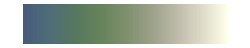
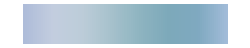
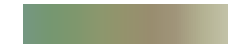
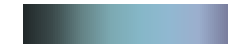
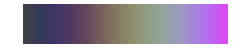
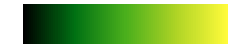
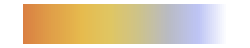
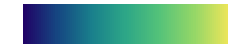

```mathematica
GraphicsGrid[Partition[ColorData[#,"Image"]&/@ColorData["Gradients"],3],ImageSize->300]
```

Vykreslení 3D grafu pomocí příkazu ColorFunction a přidání legendy grafu.

```mathematica
Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10},
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic
]
```

-Graphics3D-

Vykreslování 3D grafu podle osy “z”  (barvy pro osy “x” a ”y” jsou nastaveny staticky)	.

```mathematica
graf1=Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10},ColorFunction->Function[{x,y,z},Hue[z]]
]
```

-Graphics3D-

Graf nemusí být vykreslován pouze pomocí barvy ale také pomocí vrstevnic.

```mathematica
Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10},
PlotTheme->"Web"
]
```

-Graphics3D-

Vybarvení jednotlivých polích 3D grafu pomocí příkazu MeshShading. Výsledný graf je také doplněn o popisky os AxesLabel a název grafu PlotLabel.

```mathematica
Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10},
MeshShading->{{Blue,Purple},{Green,Orange}},
AxesLabel->{"osa x","osa y","osa z"},
PlotLabel->"Graf"
]
```

-Graphics3D-

Pomocí příkazu PlotStyle můžeme definovat barvu pro každý vykreslovaný graf zvlášť.

```mathematica
Plot3D[{Sin[x],Cos[x]},{x,0,2Pi},{y,0,2Pi},
PlotStyle->{Orange,Purple}
]
```

-Graphics3D-

Nastavení výchozího pohledu na zobrazený graf ze předu (Front), z vrchu (Top).

```mathematica
Plot3D[Sin[x ]^2-Cos[y]^2,{x,0,5},{y,0,3},
ViewPoint->Front
]
```

-Graphics3D-

Nastavení výchozího pohledu na zobrazený graf pomocí souřadnic.

```mathematica
Plot3D[Sin[x ]^2-Cos[y]^2,{x,0,5},{y,0,3},
ViewPoint->{3,-5,3}
]
```

-Graphics3D-

Využití mřížky pro 3D graf.

```mathematica
Plot3D[Sin[x ]^2-Cos[y]^2,{x,0,5},{y,0,3},
FaceGrids->All
]
```

-Graphics3D-

Definování mřížky jen z vybraných stran pomocí příkazu FaceGrids. Nastavení stylů vykreslované mřížky pomocí příkazu FaceGridsStyle.

```mathematica
Plot3D[Sin[x ]^2-Cos[y]^2,{x,0,5},{y,0,3},
FaceGrids->{{0,0,-1},{0,1,0}},
FaceGridsStyle->Directive[Blue,Dotted,Thickness@0.007]
]
```

-Graphics3D-

Vykreslování 3D grafu můžeme měnit pomocí několika příkazů. 
Příkaz Background mění barevné pozadí grafu. 
Příkaz BoundaryStyle mění styl hranice grafu. 
Příkaz Filling se využívá k vyplnění plochy kolem grafu. 
Pomocí příkazu FillingStyle můžeme měnit styly (Filling) barva atd. 
Příkaz Mesh určuje měřítko mřížky na grafu. 
Příkaz MeshStyle určuje styl mřížky. 
Pomocí příkazu PlotLegend můžeme nastavit popis legendy. 
Příkaz Opacity určuje průhlednost grafu.

```mathematica
Plot3D[Sin[x ]^2-Cos[y]^2,{x,0,5},{y,0,3},
Background->Gray,
BoundaryStyle->Directive[Red,Thick],
Filling->Bottom,
FillingStyle->Purple,
Mesh->5,
MeshStyle->Red,
PlotLegends->{"graf"},
PlotStyle->Opacity[0.7]
]
```

-Graphics3D-

Funkce ListPointPlot3D[]

Funkce ListPlot3D je obdobná funkci ListPlot. Vstupní data musí být ve tvaru:
	{{x_1, y_1,z_1}, {x_2, y_2,z_2}, ... {x_n, y_n,z_n}}

V kombinaci s funkcí Show můžeme spojit bodový a spojitý graf podobně jako u kombinace Plot a ListPlot.

```mathematica
ListPointPlot3D[{{1,1,1},{1,2,2},{2,1,2},{2,2,4}}]
```

-Graphics3D-

Data můžeme opět generovat pomocí funkce Table.

Pozn.: Výsledná data musíme pro funkci ListPointPlot3D “správně naformátovat”.

```mathematica
data=Table[{x,y,x+y},{x,1,5,0.5},{y,1,5,0.5}];
data=Flatten[data,1];
ListPointPlot3D[data]
```

-Graphics3D-

Podobně jako u každého grafu, i zde můžeme zobrazit více funkcí najednou.

```mathematica
data1=Table[{x,y,(x+y)^2},{x,1,5,0.5},{y,1,5,0.5}];
data1=Flatten[data1,1];
ListPointPlot3D[{data,data1}]
```

-Graphics3D-

### Filling

Vyplňení oblasti, kterou zabírají data (body).
Má podobné nastavení a vlastnosti jako u 2D grafu.

```mathematica
ListPointPlot3D[data,
Filling->Bottom
]
```

-Graphics3D-

```mathematica
(* v případě, že chceme upřesnit vykreslení, je třeba uvést i barvu výplně! *)
ListPointPlot3D[{data,data1},
Filling->{1->{Bottom,Red},2->{Top,Blue}}
]
```

-Graphics3D-

### PlotStyle

Nastavení vzhledu grafu (bodů).

```mathematica
ListPointPlot3D[data,
PlotStyle->Red
]
```

-Graphics3D-

```mathematica
ListPointPlot3D[data,
PlotStyle->Directive[
Red,
PointSize->0.05(*velikost bodu*),
Opacity@0.5(*pruhlednost*)
]
]
```

-Graphics3D-

Funkce Show[] (pro 3D)

Podobně jako u 2D; umožňuje kombinovat například grafy. Veškeré nastavení a chování je takřka totožné.

```mathematica
(* vytvořím graf 3D *)
graf1=Plot3D[Sin[x]*Cos[(x*y)/4],{x,-2π,2π},{y,-2π,2π}]
```

-Graphics3D-

```mathematica
(*vytvořím druhá 3D graf*)
data2=Table[{x,y,Sin[x]*Cos[(x*y)/4]},{x,-2π,2π,0.5},{y,-2π,2π,0.5}];
data2=Flatten[data2,1];
graf2=ListPointPlot3D[data2]
```

-Graphics3D-

```mathematica
Show[graf1,graf2]
```

-Graphics3D-

Pozn.: Veškeré nastavení je stejné jako u 2D.

ContourPlot[] (Obrysový graf)

-Graphics3D-

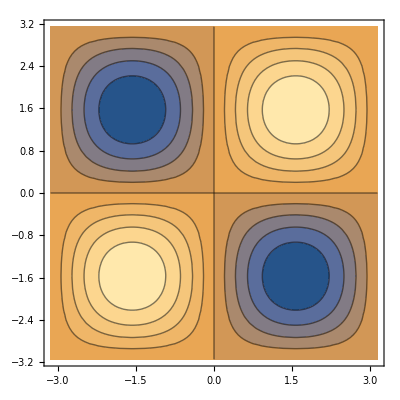

```mathematica
(*pro srovnání je zde uveden i výstup 3D grafu*)
Plot3D[Sin[x]*Sin[y],{x,-π,π},{y,-π,π}]
ContourPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π}]
```

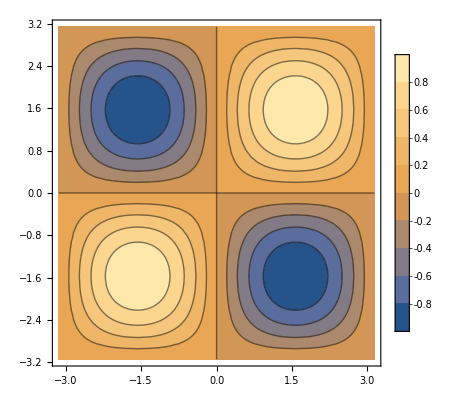

```mathematica
(*většina nastavení je stejná jako u ostatních grafů, např. PlotLegends*)
ContourPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π},PlotLegends->Automatic]
```

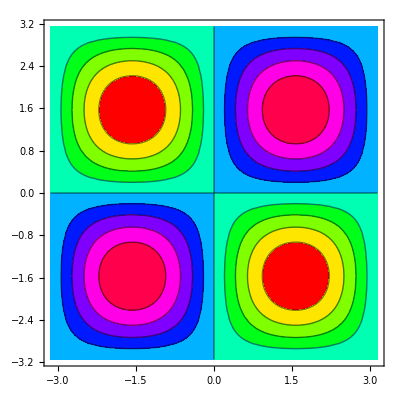

```mathematica
(*můžeme měnit vzhled (barevnou kombinaci)*)
ContourPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π},ColorFunction->Hue]
```

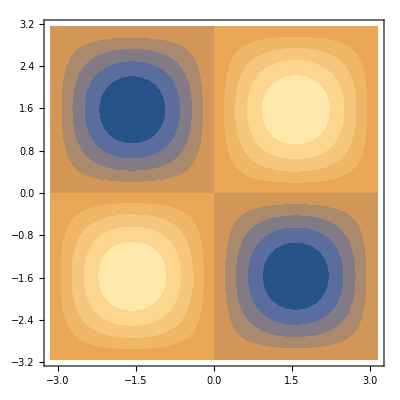

```mathematica
(*vypnout vrstevnice*)
ContourPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π},ContourLines->False]
```

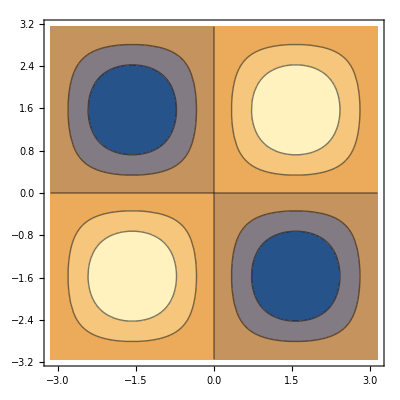

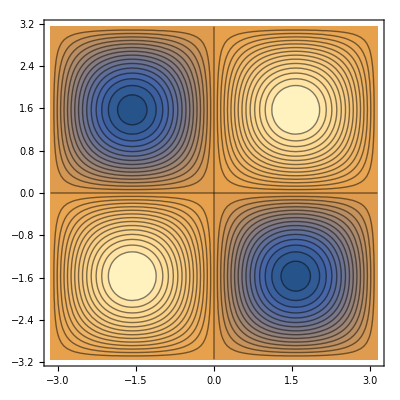

```mathematica
(*změnit rozlišení, pozor: vysoké hodnoty zvyšují kvalitu, ale i více zatěžují procesor*)
ContourPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π},Contours->5]
ContourPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π},Contours->30]
```

DensityPlot[] (Graf hustoty)

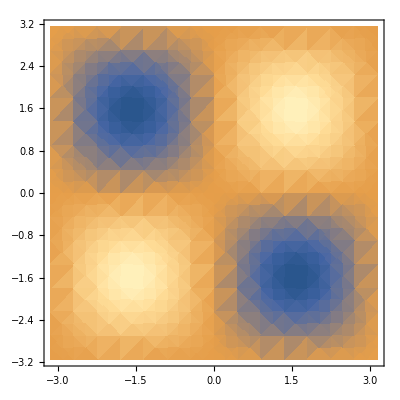

```mathematica
(*podobný obrysovému grafu*)
DensityPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π}]
```

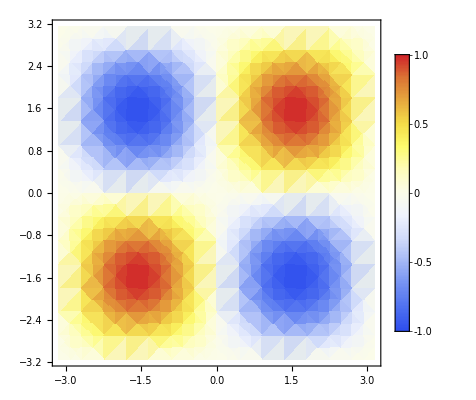

```mathematica
(*opět je většina nastavení stejná jako u ostatních, nám známých grafů*)
DensityPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π},ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

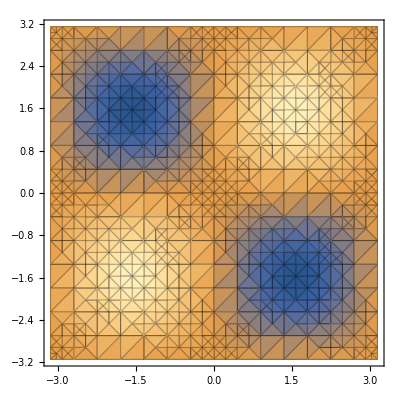

```mathematica
(*zobrazení mřížky*)
DensityPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π},Mesh->All]
```

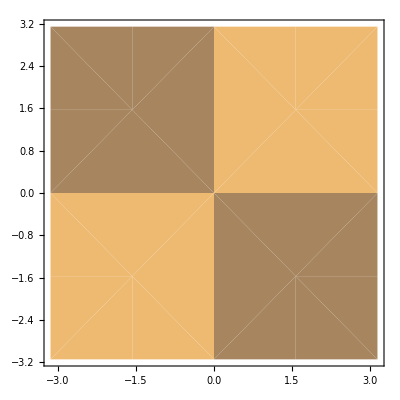

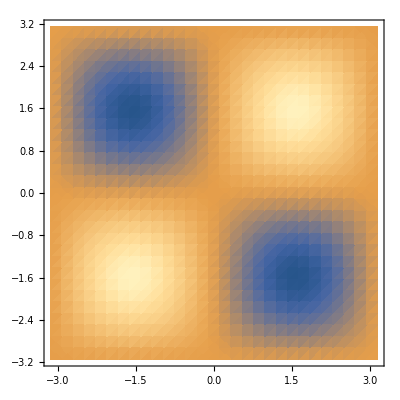

```mathematica
(*kvalita*)
DensityPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π},PlotPoints->2]
DensityPlot[Sin[x]*Sin[y],{x,-π,π},{y,-π,π},PlotPoints->30]
```

BarChart[] (Sloupcový graf)

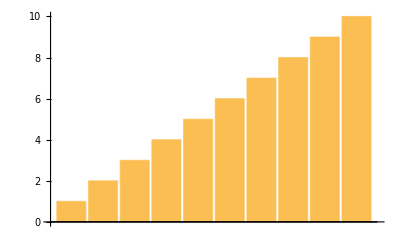

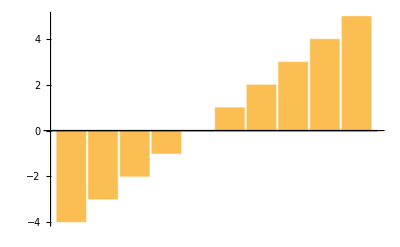

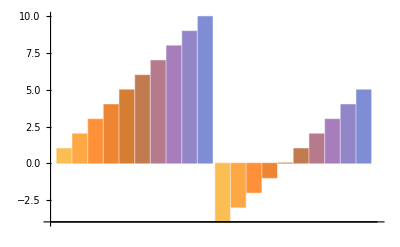

```mathematica
(*statistický graf, nejprve si vygenerujeme hodnoty*)
v1=Range@10;
v2=v1-5;
BarChart[v1]
BarChart[v2]
BarChart@{v1,v2}
```

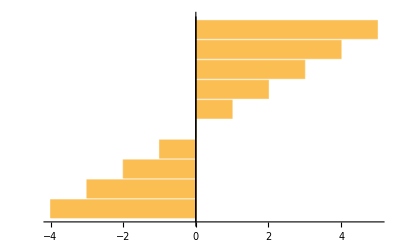

```mathematica
(*počátek sloupců*)
BarChart[v2,BarOrigin->Left]
```

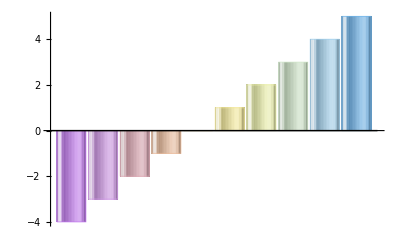

```mathematica
(*styl sloupců*)
BarChart[v2,ChartElementFunction->"GlassRectangle",ChartStyle->"Pastel"]
```

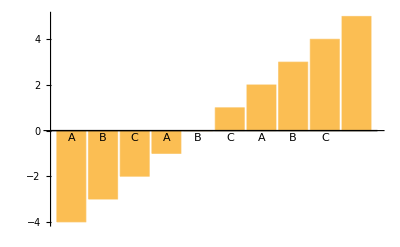

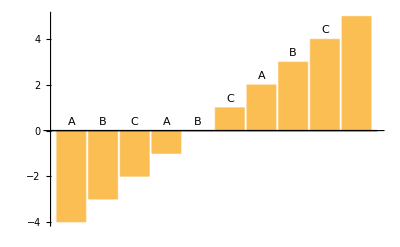

```mathematica
(*popisy*)
BarChart[v2,ChartLabels->{"A","B","C","A","B","C","A","B","C"}]
BarChart[v2,ChartLabels->Placed[{"A","B","C","A","B","C","A","B","C"},Above]]
```

PieChart[] (Koláčový graf)

```mathematica
(*obdobný sloupcovému grafu*)
PieChart[v2]
PieChart[{v1,v2}]
```

-Graphics-

-Graphics-

```mathematica
(*3D verze*)
PieChart3D[{v1,v2}]
```

-Graphics3D-

```mathematica
(*vzhled a popisky podobně jako u sloupcového grafu*)
PieChart[v2,ChartElementFunction->"NoiseSector",ChartStyle->{Red, Green, Blue, Yellow,Orange}]
```

-Graphics-

Histogram[]

Graf hodně se podobající funkci BarChart[].
Jeden ze základních statistických grafů.
používá se na zobrazení rozložení hodnot (jejich frekvence).

Na ose “x” je vždy rozsah hodnot a na ose “y” je jejich počet. 

Pozn.: Vlastnosti téměř totožné s funkcí BarChart[].

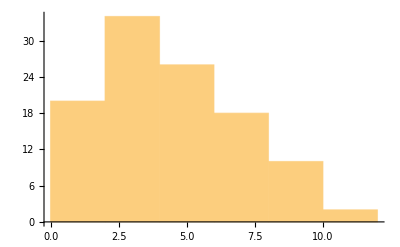

```mathematica
hisData=Flatten@Table[Range[Abs@i],{i,-10,10}];
Histogram[hisData]
```

### ChartElementFunction

Nastavuje “vzhled“ sloupců.

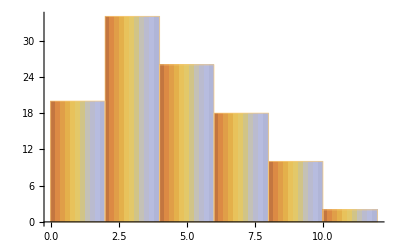

```mathematica
Histogram[hisData,ChartElementFunction->"GradientRectangle"]
```

### ChartElements

Můžete nastavit i libovolný objekt pro zobrazení sloupců.

```mathematica
Histogram[hisData,ChartElements->Graphics[Disk[]]]
```

-Graphics-

```mathematica
Histogram[hisData,ChartElements->Graphics[{Red,Triangle[]}]]
```

-Graphics-

### ChartLegends

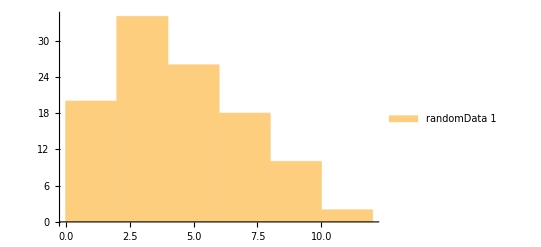

```mathematica
Histogram[hisData,ChartLegends->{"randomData 1"}]
```

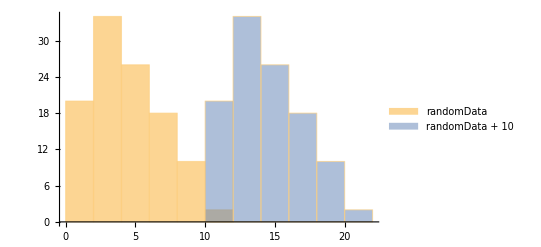

```mathematica
Histogram[{hisData,hisData+10},
ChartLegends->{"randomData","randomData + 10"}
]
```

### ChartStyle

Nastavení stylu sloupců (barva, průhlednost, okraje, ...)

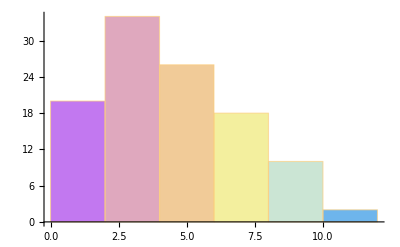

```mathematica
Histogram[hisData,ChartStyle->"Pastel"]
```

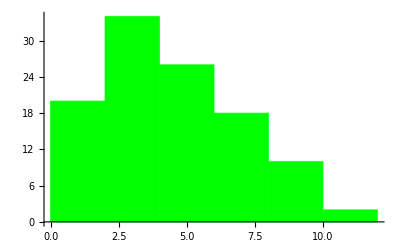

```mathematica
Histogram[hisData,
ChartStyle->Green
]
```

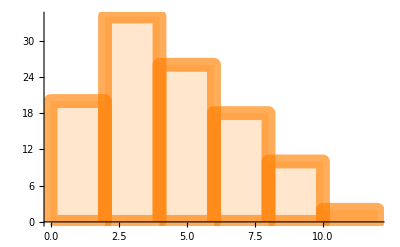

```mathematica
Histogram[hisData,
ChartStyle->Directive[
(*styl okrajů*)EdgeForm[{Orange,Dashed,Thickness@0.025}],
 LightOrange
]
]
```

## Samostatné úkoly

1.)

Vytvořte graf (viz obrázek) kombinací dvou grafů (Plot3D[] a ListPointPlot3D[]) pro funkci Sin[x+y]